```mathematica
pp[z_,k_]:=Product[z-j,{j,0,k-1}]
Table[j!pp[z,j+1]Sum[(-1)^k/(z-k) StirlingS2[j,k]k!/j!,{k,0,Infinity}],{j,0,10}]//TableForm
```

1
((-1+z) z)/(1-z)
z^2
-z^2 (1+z)
z^3 (5+z)
-z^2 (-4+11 z+16 z^2+z^3)
-z (42 z^2-119 z^3-42 z^4-z^5)
-z (120 z-398 z^2+141 z^3+757 z^4+99 z^5+z^6)
-z (-2160 z^2+7250 z^3-6189 z^4-3721 z^5-219 z^6-z^7)
-z (-12096 z+45624 z^2-41186 z^3-41171 z^4+72976 z^5+15706 z^6+466 z^7+z^8)
-z (332640 z^2-1261788 z^3+1594648 z^4-371569 z^5-595760 z^6-60082 z^7-968 z^8-z^9)

```mathematica
pp[z,5]/.z->2.5
```

1.40625

```mathematica
FactorialPower[z,5]/.z->2.5
```

1.40625

```mathematica
FullSimplify[1/Gamma[z]/Gamma[1-z]]
```

Sin[π z]/π

```mathematica
Sum[StirlingS2[j,k]k!/j! Log[1+x]^j,{j,0,Infinity}]/.x->.307/.k->4
```

0.00888287

```mathematica
.307^4
```

0.00888287

```mathematica
FullSimplify@(1/Gamma[z]/Gamma[1-z]) Sum[(-1)^k/(z-k)x^k,{k,0,Infinity}]
```

-(HurwitzLerchPhi[-x,1,-z] Sin[π z])/π

```mathematica
-(HurwitzLerchPhi[-x,1,-z] Sin[π z])/π/.z->3.0000000001/.x->10
```

999.999

```mathematica
10^1.5
```

31.6228

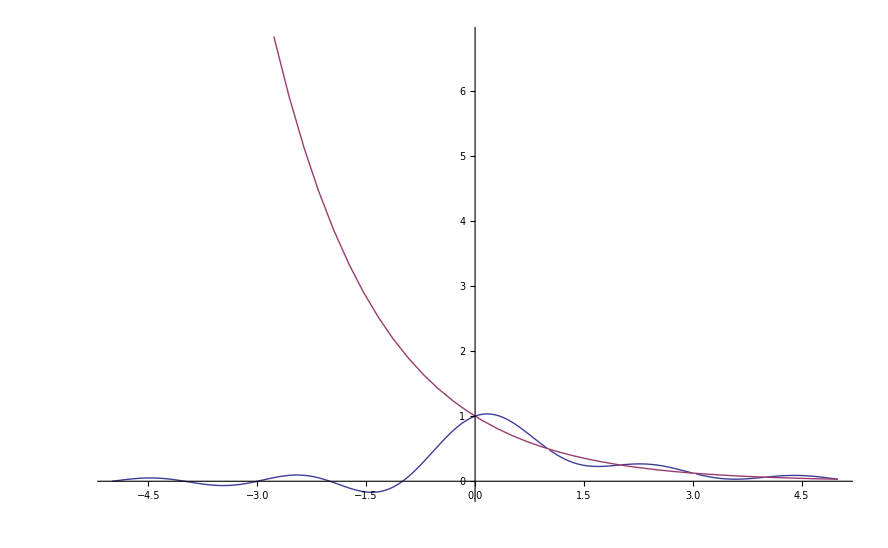

```mathematica
Plot[{-(HurwitzLerchPhi[-.5,1,-z] Sin[π z])/π,.5^(z)},{z,-5,5}]
```

```mathematica
Series[-(HurwitzLerchPhi[-x,1,-z] Sin[π z])/π,{z,0,20}]
```

HurwitzLerchPhi[-x,1,-z] (-z+(π^2 z^3)/6-(π^4 z^5)/120+(π^6 z^7)/5040-(π^8 z^9)/362880+(π^10 z^11)/39916800-(π^12 z^13)/6227020800+(π^14 z^15)/1307674368000-(π^16 z^17)/355687428096000+(π^18 z^19)/121645100408832000+O[z]^21)

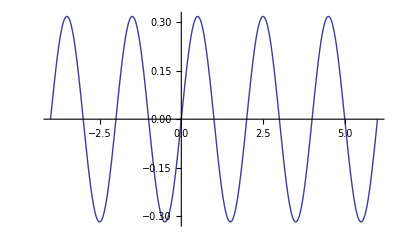

```mathematica
Plot[{Sin[π z]/π},{z,-4,6}]
```

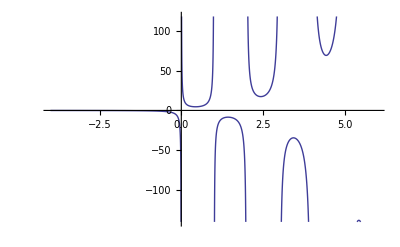

```mathematica
Plot[-HurwitzLerchPhi[-2,1,-z] ,{z,-4,6}]
```

```mathematica
Sum[(1/Gamma[z]/Gamma[1-z])(-1)^k/(z-k)x^k/.z->3.5/.x->.5,{k,0,Infinity}]
```

0.033875

```mathematica
.5^3.5
```

0.0883883

```mathematica
pp[z_,k_]:=Product[z-j,{j,0,k-1}]
Table[j!pp[z,j+1]Sum[(-1)^k/(z-k) StirlingS2[j,k]k!/j!,{k,0,Infinity}],{j,0,10}]//TableForm
```

1
((-1+z) z)/(1-z)
z^2
-z^2 (1+z)
z^3 (5+z)
-z^2 (-4+11 z+16 z^2+z^3)
-z (42 z^2-119 z^3-42 z^4-z^5)
-z (120 z-398 z^2+141 z^3+757 z^4+99 z^5+z^6)
-z (-2160 z^2+7250 z^3-6189 z^4-3721 z^5-219 z^6-z^7)
-z (-12096 z+45624 z^2-41186 z^3-41171 z^4+72976 z^5+15706 z^6+466 z^7+z^8)
-z (332640 z^2-1261788 z^3+1594648 z^4-371569 z^5-595760 z^6-60082 z^7-968 z^8-z^9)

```mathematica
FullSimplify@Sum[(-1)^k StirlingS2[7,k]k!/7!/(z-k)/Gamma[z]/Gamma[1-z],{k,1,7}]
```

-(z (1+z) (120+z (-518+z (659+z (98+z)))) Sin[π z])/(5040 π (-7+z) (-6+z) (-5+z) (-4+z) (-3+z) (-2+z) (-1+z))

```mathematica
FullSimplify@Sum[7!/Gamma[z-7]/Gamma[1-z](-1)^k StirlingS2[7,k]k!/7!/(z-k),{k,1,7}]
```

-(z (1+z) (120+z (-518+z (659+z (98+z)))) Sin[π z])/π

```mathematica
Sum[(-1)^k/(z-k) StirlingS2[j,k]k!/j!,{k,0,7}]/.j->7
```

-1/(-7+z)+3/(-6+z)-10/(3 (-5+z))+5/(3 (-4+z))-43/(120 (-3+z))+1/(40 (-2+z))-1/(5040 (-1+z))

```mathematica
1/pp[z-1,7]/.z->3.3
```

0.0937767

```mathematica
Gamma[z-7]/Gamma[z]/.z->3.3
```

0.0937767

```mathematica
Table[Limit[Sum[(-1)^k StirlingS2[j,k]k!/j!/(z-k)/Gamma[z]/Gamma[1-z],{k,0,j}],z->3],{j,0,10}]//TableForm
```

0
0
0
1
3/2
5/4
3/4
43/120
23/160
605/12096
311/20160

```mathematica
Series[(E^x-1)^(3),{x,0,10}]
```

x^3+(3 x^4)/2+(5 x^5)/4+(3 x^6)/4+(43 x^7)/120+(23 x^8)/160+(605 x^9)/12096+(311 x^10)/20160+O[x]^11

```mathematica
Gamma[3]
```

2

```mathematica
Sum[(-1)^k StirlingS2[j,k]k!/j!/(z-k)/Gamma[z]/Gamma[1-z],{k,0,j}]
```

∑_(k=0)^j ((-1)^k k! StirlingS2[j,k])/((-k+z) j! Gamma[1-z] Gamma[z])

```mathematica
Sum[(-1)^k (1/k! Sum[(-1)^i Binomial[k,i](k-i)^j,{i,0,k}])k!/j!/(z-k)/Gamma[z]/Gamma[1-z],{k,0,j}]
```

∑_(k=0)^j ((-1)^k k! StirlingS2[j,k])/((-k+z) j! Gamma[1-z] Gamma[z])

```mathematica
Sum[(-1)^k (1/k! Sum[(-1)^i Binomial[k,i](k-i)^j,{i,0,k}])k!/j!/(z-k)/Gamma[z]/Gamma[1-z],{k,0,j}]/.j->3/.z->4.2
```

-0.0806151

```mathematica
Sum[(-1)^k (Sum[(-1)^i Binomial[k,i](k-i)^j,{i,0,k}])/j!/(z-k)/Gamma[z]/Gamma[1-z],{k,0,j}]/.j->3/.z->4.2
```

-0.0806151

```mathematica
Sum[(Sum[(-1)^k (-1)^i Binomial[k,i](k-i)^j/j!/(z-k)/Gamma[z]/Gamma[1-z],{i,0,k}]),{k,0,j}]/.j->3/.z->4.2
```

-0.0806151

```mathematica
Sum[(-1)^k (-1)^i Binomial[k,i](k-i)^j/j!/(z-k)/Gamma[z]/Gamma[1-z],{k,0,j},{i,0,k}]/.j->3/.z->4.2
```

-0.0806151

```mathematica
Sum[(-1)^k (-1)^i Binomial[k,i](k-i)^j/j!/(z-k)/Gamma[z]/Gamma[1-z],{k,0,j},{i,0,k}]/.j->3/.z->4.2
```

```mathematica
Sum[(-1)^k (-1)^i Binomial[k,i](k-i)^j/j!/(z-k)/Gamma[z]/Gamma[1-z],{k,0,j},{i,0,k}]
```

∑_(k=0)^j ∑_(i=0)^k -((-1)^(i+k) (-i+k)^j Binomial[k,i] Sin[π z])/(π (k-z) j!)

```mathematica
Expand@FullSimplify@Table[j!pp[z,j+1] Sum[(-1)^k/(z-k) StirlingS2[j,k]k!/j!,{k,0,2j}],{j,0,10}]//TableForm
```

1
-z
z^2
-z^2-z^3
5 z^3+z^4
4 z^2-11 z^3-16 z^4-z^5
-42 z^3+119 z^4+42 z^5+z^6
-120 z^2+398 z^3-141 z^4-757 z^5-99 z^6-z^7
2160 z^3-7250 z^4+6189 z^5+3721 z^6+219 z^7+z^8
12096 z^2-45624 z^3+41186 z^4+41171 z^5-72976 z^6-15706 z^7-466 z^8-z^9
-332640 z^3+1261788 z^4-1594648 z^5+371569 z^6+595760 z^7+60082 z^8+968 z^9+z^10

```mathematica
Sum[Sin[Pi z]/Pi (-1)^k/(z-k) (-1)^(k-j) Binomial[k,j],{k,0,Infinity}]
```

((-1)^-j Binomial[0,j] HypergeometricPFQ[{1,1,-z},{1-j,1-z},1] Sin[π z])/(π z)

```mathematica
Limit[((-1)^-j Binomial[0,j] HypergeometricPFQ[{1,1,-z},{1-j,1-z},1] Sin[π z])/(π z),z->3]
```

Limit[((-1)^-j Binomial[0,j] HypergeometricPFQ[{1,1,-z},{1-j,1-z},1] Sin[π z])/(π z),z→3]

```mathematica
N@Limit[Sum[Sin[Pi z]/Pi (-1)^k/(z-k) (-1)^(k-j) Binomial[k,j],{k,0,Infinity}]/.z->3.3,j->4]
```

$Aborted